```mathematica
(* Generalized Burgers with stacked  normal sheets in  normal direction *)
```

```mathematica
NSEq[VV_,PP_,R_] := Nu Laplacian[VV,R] - Grad[VV,R].VV - Grad[PP,R];
```

```mathematica
V = {-G'[z/Nu] x/Nu ,S[z/Nu], G[z/Nu]};
```

```mathematica
P =  H[z/Nu] - s x^2/2/Nu^2;
```

```mathematica
R = {x,y,z};
```

```mathematica
Div[V,R]
```

0

```mathematica
Omega = Curl[V,R]
```

{-S'[z/Nu]/Nu,-(x G''[z/Nu])/Nu^2,0}

```mathematica
EQ = NSEq[V,P,R]//Simplify
```

{(x (s-G'[z/Nu]^2+G[z/Nu] G''[z/Nu]-G^(3)[z/Nu]))/Nu^2,(-G[z/Nu] S'[z/Nu]+S''[z/Nu])/Nu,-(G[z/Nu] G'[z/Nu]+H'[z/Nu]-G''[z/Nu])/Nu}

```mathematica
EqG = (Nu^2EQ[[1]]/x)/.z -> ξ Nu//Simplify
```

s-G'[ξ]^2+G[ξ] G''[ξ]-G^(3)[ξ]

```mathematica
Sub = G'[ξ] -> f[G[ξ]^2];
```

```mathematica
(*DSolve[EqG==0,G[ξ],ξ]*)
```

```mathematica
EqS =Nu EQ[[2]]/.z -> ξ Nu//Simplify
```

-G[ξ] S'[ξ]+S''[ξ]

```mathematica
EqG
```

s-G'[ξ]^2+G[ξ] G''[ξ]-G^(3)[ξ]

```mathematica
ClearAll[Gnp];
Gnp[0]:=g;
Gnp[n_?Positive]:=f[g^2]D[Gnp[n-1],g];
```

```mathematica
Eqf =EqG//.{G[ξ]->Gnp[0],Derivative[n_][G][ξ]->Gnp[n]}//Factor
```

s-f[g^2]^2+2 g^2 f[g^2] f'[g^2]-2 f[g^2]^2 f'[g^2]-4 g^2 f[g^2] f'[g^2]^2-4 g^2 f[g^2]^2 f''[g^2]

```mathematica
Eqf0 = (Eqf//Expand)/.g->Sqrt[w]//Expand
```

s-f[w]^2+2 w f[w] f'[w]-2 f[w]^2 f'[w]-4 w f[w] f'[w]^2-4 w f[w]^2 f''[w]

```mathematica
Eqf00 =1/f[w] Eqf0/.s->0//Expand
```

-f[w]+2 w f'[w]-2 f[w] f'[w]-4 w f'[w]^2-4 w f[w] f''[w]

```mathematica
Gnp[2]/.g->Sqrt[w]
```

2 √w f[w] f'[w]

```mathematica
DSolve [G'[ξ] == f[G[ξ]^2],G[ξ],ξ]
```

{{G[ξ]→InverseFunction[1/f[K[1]^2]K[1]1#1&][ξ+C[1]]}}

```mathematica
Fapp[x_, ff_, M_] :=Module[
{ffs=Table[ff[k],{k,0,M}], w =1(1+x)/2},
(w - 1)/2  ( 1+(x-1)(Table[ChebyshevT[n,x ],{n,0,M}].ffs))];
```

```mathematica
ClearAll[Energy,EnergyFactory];
EnergyFactory[M_,ff_]:=Module[{fapp, Eqf0r},
fapp=Fapp[x, ff, M] ;
Eqf0r=Eqf00/.{
f[w]->fapp,
Derivative[k_][f][w]:>(2)^k D[fapp,{x,k}],
w ->(1 + x)/2
};
Integrate[Eqf0r^2,{x,-1,1}]
]
```

```mathematica
EnergyFactory[1, ff]
```

2/3-(4 ff[0])/3+(8 ff[0]^2)/3-(32 ff[0]^3)/5+(32 ff[0]^4)/5-(8 ff[1])/15-8/3 ff[0] ff[1]+128/7 ff[0]^2 ff[1]-904/35 ff[0]^3 ff[1]+(472 ff[1]^2)/105-948/35 ff[0] ff[1]^2+4952/105 ff[0]^2 ff[1]^2+(1124 ff[1]^3)/105-1304/35 ff[0] ff[1]^3+(1192 ff[1]^4)/105

```mathematica
ClearAll[Sol];
Sol[M_] := Module[
{Energy},
Energy =EnergyFactory[M,ff];
 NMinimize[Energy,Evaluate[Table[ff[k],{k,0,M}]]]
];
```

```mathematica
(*SS2 =Sol[2]*)
```

```mathematica
(*f0 [w_] = Fapp[ 2 w-1, ff, 5]/.SS5[[2]]*)
```

```mathematica
Plot[f0[w],{w,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Test[M_] :=
Module[{fapp,Eq},
fapp=Fapp[2 w -1, ff, M]/.SS5[[2]] ;
Eq=Eqf00/.{
f[w]->fapp,
Derivative[k_][f][w]:> D[fapp,{w,k}]
};
Plot[{Eq ,fapp},{w,0,1},PlotLegends->"Expressions", PlotRange->All]
];
```

```mathematica
(*Test[5]*)
```

```mathematica
Eqf00
```

-f[w]+2 w f'[w]-2 f[w] f'[w]-4 w f'[w]^2-4 w f[w] f''[w]

```mathematica
ClearAll[Sol];Sol[w0_]:=NDSolve[{Eqf00==0,f[w0]==0,f'[w0] ==1/2},f,{w,w0,1}][[1,1]]
```

```mathematica
Sol[1/2]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NDSolve::ndnum: Encountered non-numerical value for a derivative at w == 0.5.

-f[w]+2 w f'[w]-2 f[w] f'[w]-4 w f'[w]^2-4 w f[w] f''[w]==0

```mathematica
Plot[f[w]/.Sol,{w,0.025,0.27},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.025005} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Eqf00/.{f[w] -> a w,f'[w] ->a,f''[w]-> 0 }//Simplify
```

(1-6 a) a w

```mathematica
SubAB[A_, B_] := { A -> B, D[A,w] ->D[B,w],D[A,{w,2}]-> D[B,{w,2}] }
```

```mathematica
fas = a (w0- w)^(1/2)  + b  (w0- w)   + c(w0-w)^(3/2);
```

```mathematica
EEX=CoefficientList[ Assuming[x>0,Normal[(Simplify[Eqf0/.SubAB[f[w],fas]]/.{w -> w0 - x^2} )+ O[x]^4]],x]
```

{s-a^2 w0-3 a^2 b w0,a^3-3 a b w0-7 a b^2 w0-8 a^2 c w0,7 a^2 b-2 b^2 w0-4 b^3 w0-4 a c w0-26 a b c w0,a b+12 a b^2+13 a^2 c-5 b c w0-19 b^2 c w0-20 a c^2 w0}

```mathematica
Solve[#==0& /@EEX[[;;2]],{b,c}][[1]]//Simplify
```

{b→1/3 (-1+s/(a^2 w0)),c→(-7 s^2+5 a^2 s w0+a^4 w0 (9 a^2+2 w0))/(72 a^5 w0^2)}

```mathematica
fas0 = a (w- w0)  + b  (w- w0)^3   + c(w-w0)^3;
EEX0=CoefficientList[ Assuming[x>0,Normal[(Simplify[Eqf0/.SubAB[f[w],fas0]]/.{w -> w0 + x} )+ O[x]^4]],x]
```

{s,2 a^2 w0-4 a^3 w0,a^2-6 a^3,8 a (b+c) w0-52 a^2 (b+c) w0}

```mathematica
Solve[#==0& /@EEX0[[;;2]],{s,a,c}]//Simplify
```

{{s→0,a→0},{s→0,a→1/2}}

```mathematica
(**
```

```mathematica
ClearAll[Sols];Sols[G_] :=DSolve[{EqS==0,S[0]==0},S[ξ],ξ][[1,1]]/.{C[1]-> 1, K[1]->w, K[2]->u}
```

```mathematica
EqH = Nu EQ[[3]]/.z -> ξ Nu//Simplify
```

-G[ξ] G'[ξ]-H'[ξ]+G''[ξ]

```mathematica
DSolve[EqH==0,H[ξ],ξ][[1,1]]
```

H[ξ]→C[1]-G[ξ]^2/2+G'[ξ]

```mathematica
(* -G'[z]^2+G[z] G''[z]-Nu G^(3)[z]*)
```

```mathematica
SolG[L_] := NDSolve[{(EqG/.s->0)==0,G[-L]==1, G[L]==-1,G[0]==0}, G,{ξ,-L,L}][[1,1]]
```

```mathematica
G1 =G/.SolG[10]
```

InterpolatingFunction[…]

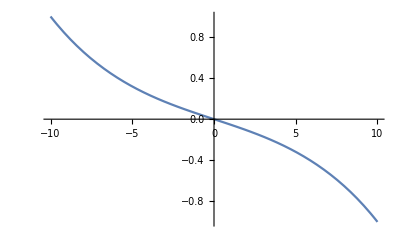

```mathematica
Plot[G1[ξ],{ξ,-10,10},PlotRange->All]
```

```mathematica
NIntegrate[G1[ξ]^2,{ξ,-10,10}]
```

4.40718

```mathematica
Nu Curl[V,R]/. z -> Nu ξ
```

{-S'[ξ],-(x G''[ξ])/Nu,0}

```mathematica
NSol[L_] := 
Module[{G1,F1,S1},
G1 = G/.NDSolve[{(EqG/.s->0)==0,G[-L]==1, G[L]==-1,G[0]==0}, G,{ξ,-L,L}][[1,1]];
F1 = F/.NDSolve[{F'[ξ] == G1[ξ],F[0] ==0} ,F,{ξ,-L,L}][[1,1]];
S1 = S/.NDSolve[{S'[ξ] ==Exp[F1[ξ] ],S[0]==0},S,{ξ,-L,L}][[1,1]];
{ G1,S1}
 ];
```

```mathematica
GSSol = NSol[11]
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

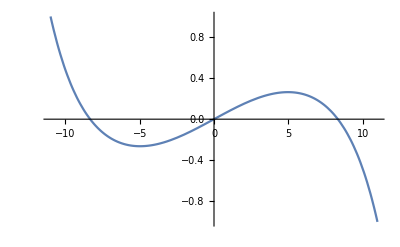

```mathematica
Plot[GSSol[[1]][ξ],{ξ,-11,11},PlotRange->All]
```

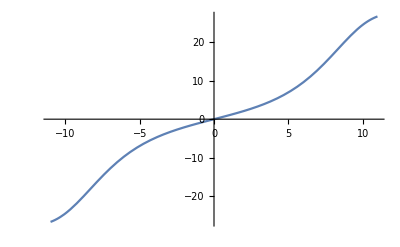

```mathematica
Plot[GSSol[[2]][ξ],{ξ,-11,11}]
```

```mathematica
S1 = GSSol[[2]];
```

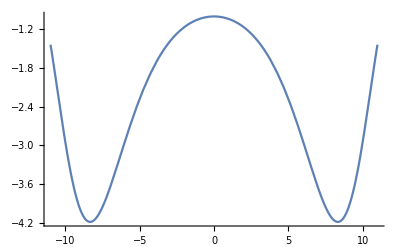

```mathematica
Plot[-S1'[z],{z,-11,11}]
```

```mathematica
G2 = GSSol[[1]]
```

InterpolatingFunction[…]

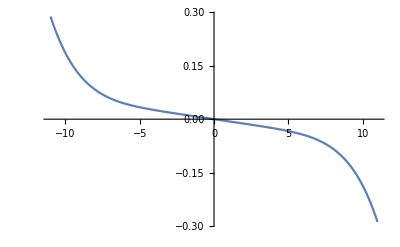

```mathematica
Plot[G2''[z],{z,-11,11}]
```